```mathematica
求根
```

```mathematica
r=52.4231;
FindRoot[{η^2+ξ^2==r,η+ξ Cot[ξ]==0},{ξ,2.5},
{η,6.8}]
FindRoot[{η^2+ξ^2==r,η+ξ Cot[ξ]==0},{ξ,5.5},
{η,4.8}]
Clear[r]
```

{4000→2.75174,η→6.69709}

{4000→5.43429,η→4.78452}

```mathematica
((1.0546*10^-34)^2)/(2*9.11*10^-31*10^-18*1.6*10^-19)
```

0.0381511

```mathematica
(2*9.11*10^-31*1.6*10^-19*10^-20)/((1.0546*10^-34)^2)
```

0.262116

```mathematica
计算第一个解的波函数
```

E = 0.289 eV

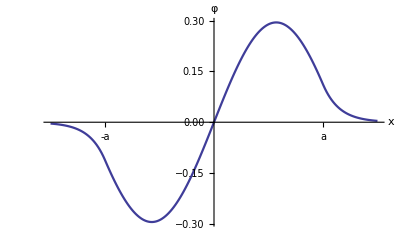

```mathematica
ξ=2.75174;a=10;V0=2;energy=3.81511*10^-2*ξ^2;Print["E = ",SetPrecision[energy,3]," eV"]
U[x_]:=If[Abs[x]≤a,0,V0]
β[x_]:=0.262116*(U[x]-energy);
s=NDSolve[{φ''[x]-β[x]*φ[x]==0,φ[0]==0,
φ'[0]==10},φ,{x,-1.5a,1.5a}];
ma=NIntegrate[φ[x]^2/.First[s],
{x,-1.5a,1.5a}];
Plot[(φ[x]/.First[s])/√ma,{x,-1.5a,1.5a},
PlotRange->All,PlotStyle->Thickness[0.004],
Ticks->{{{-a,"-a"},{a,"a"}},Automatic},
PlotPoints->200,AxesLabel->{"x","φ"},
AxesStyle->Thickness[0.003]]
Clear[ξ,a,V0,energy,U,β,s,ma,φ]
```

```mathematica
计算第二个解的波函数
```

E = 1.13eV

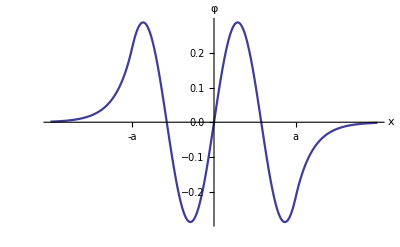

```mathematica
ξ=5.43429;a=10;V0=2;energy=3.81511*10^-2*ξ^2;Print["E = ",SetPrecision[energy,3],"eV"]
U[x_]:=If[Abs[x]≤a,0,V0];x0=2a;
β[x_]:=0.262116*(U[x]-energy);
s=NDSolve[{φ''[x]-β[x]*φ[x]==0,φ[0]==0,φ'[0]==10},φ,{x,-x0,x0}];
ma=NIntegrate[φ[x]^2/.First[s],{x,-x0,x0}];
Plot[(φ[x]/.First[s])/√ma,{x,-x0,x0},PlotRange->All,PlotStyle->Thickness[0.004],
Ticks->{{{-a,"-a"},{a,"a"}},Automatic},PlotPoints->200,AxesLabel->{"x","φ"},
AxesStyle->Thickness[0.003]]
Clear[ξ,a,V0,energy,U,β,s,ma,φ]
```